# 5.2 Renyi dimension of weighted Cantor set

## -Graphics- In this exercise, your are going to calculate and analyze the Renyi dimension spectrum of the a weighted Cantor set. The symmetric Cantor set was discussed in the lecture and you know that the box counting dimension of this set is . Recall that the Cantor set was generated by removing the middle third from the unit interval, then the remaining two subintervals had their middle thirds removed and so on. Now extend this construction by allocating a probability (or “mass”) to each subinterval at each division. Allocate of the existing probability in an interval being divided to the right-hand side of the subinterval, and to the left as is shown in the figure above.

box counting
 information dimension 
 correlation dimension

## a) Calculate analytically the Renyi dimension spectrum of the weighted Cantor set. Make sure that for , you recover the box counting dimension of the Cantor set. Give your result as a function of .

-Graphics-

## b) Using the expression derived in (a), make a plot of ​​ as a function of for .

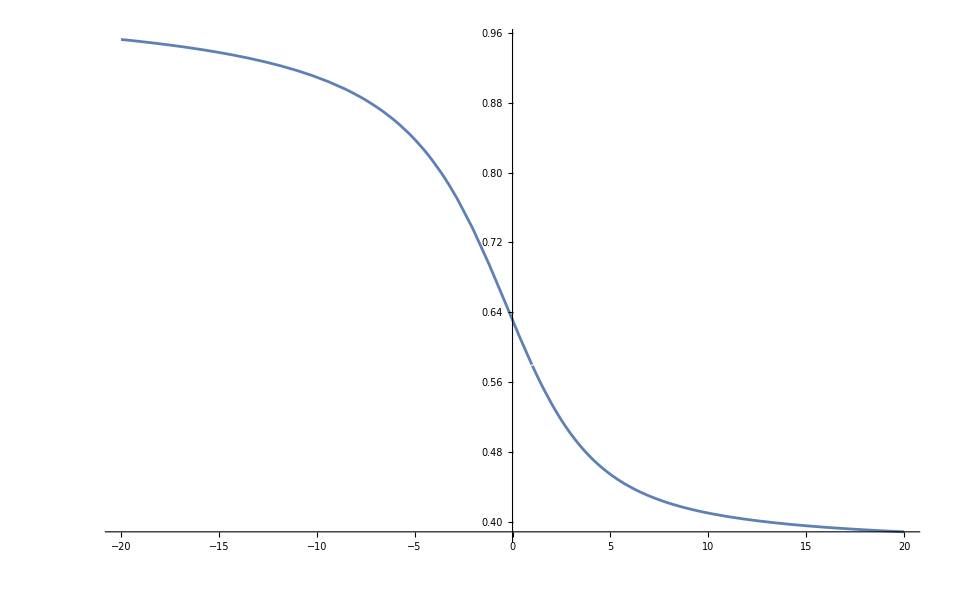

```mathematica
funcD[q_]:= 1/(1-q)*Log[p^q+(1-p)^q]/Log[3]
p=1/3;

Plot[funcD[q],{q,-20,20}]
```

## c) Using the expression derived in (a), compute explicitly (information dimension) and (correlation dimension) of the weighted Cantor set. Give your result as the vector

Since we take the limes we can use l’Hospital to calculate the “problematic” .

```mathematica
Clear[q]
nominator[q_] := Log[p^q+(1-p)^q];
denominator[q_] := (1-q)*Log[3];
derivNominator = D[nominator[q],q];
derivDenominator = D[denominator[q],q];

q = 1;
D1 = derivNominator/derivDenominator//Simplify;
q = 2;
D2 = 1/(1-q)*Log[p^q+(1-p)^q]/Log[3];
Result = {D1,D2}//TraditionalForm
```

{(log(27/4))/(log(27)),(log(9/5))/(log(3))}

## d) Using the expression derived in (a), compute explicitly and of the weighted Cantor set. Give your result as the vector .

```mathematica
Clear[q]
funcD[q_] := 1/(1-q)*Log[p^q+(1-p)^q]/Log[3]

L1 = Limit[funcD[q],q->-Infinity]//TraditionalForm;
L2 = Limit[funcD[q],q->Infinity]//TraditionalForm;

ResultD = {L1,L2}//TraditionalForm
```

{1,(log(3/2))/(log(3))}